```mathematica
ClearAll["Global`*"]
```

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
(*Bm=x[[5]];*)
Em=x[[5]];
η=x[[6]];
η2=x[[7]];
λ0=x[[8]];
ef=x[[9]];
γ=x[[10]];
ζ=x[[11]];
f0=x[[12]];
mm0=x[[13]];
χ=x[[14]];
Bm=B0*M^(-1/4);
Growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
Starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
InvaderStarvation =  N[ts*-Bm/(Em*(Log[1-f0*M^(γ-1)] + Log[M/(M*(1+χ))]))]*(1+RandomReal[{-noise,noise}]);
Mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
(*Recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);*)
Recovery =N[ ts* 1/(Em/B0*4*M^(1/4)*((1/( λ0*M^η2))+Log[1 - (1-f0*M^(γ-1))^(1/4)]))]*(1+RandomReal[{-noise,noise}]);
InvaderRecovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(1+χ)*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
Maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
InvaderMaintenance = (ts*ef*B0*(M*(1+χ))^η)*(1+RandomReal[{-noise,noise}]);
Resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{Growth,Starvation,Mortality,Recovery,Maintenance,Resourcegrowth,InvaderStarvation,InvaderRecovery,InvaderMaintenance}
);
```

```mathematica
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =M,
(*B0*)4.7*10^(-2),
(*(*Bm*)0.0245,*)
(*Em*)5774(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
GrowthOverM=RF[[1]];
StarvationOverM=RF[[2]];
MortalityOverM = RF[[3]];
MaintenanceOverM = RF[[5]];
RecoveryOverM=RF[[4]];
ResourcegrowthOverM=RF[[6]];
InvaderMaintenanceOverM=RF[[9]];
InvaderStarvationOverM=RF[[7]];
InvaderRecoveryOverM=RF[[8]];
```

```mathematica
Log[A/B]==Log[A]-Log[B]
```

Log[A/B]==Log[A]-Log[B]

```mathematica
Reduce[%]
```

Log[A]==Log[A/B]+Log[B]

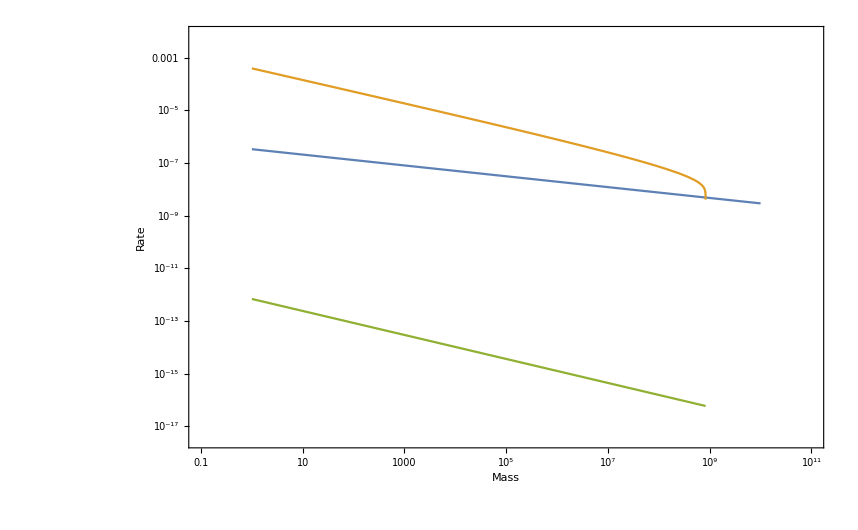

```mathematica
GrowthVStarvationPlot=LogLogPlot[{Re[GrowthOverM],StarvationOverM,RecoveryOverM},{M,1,10^10},Frame->True,FrameLabel->{"Mass","Rate"}]
```

```mathematica
RecoveryOverM
```

-(2.03498×10^-6)/(M^(1/4) (2.95168×10^6 M^0.206-1. Log[1.-1. (1.-0.0202 M^0.19)^(1/4)]))

```mathematica
Solve[Reduce[Re[GrowthOverM]==Re[StarvationOverM]],M]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[Re[1/(M^(1/4) Log[1.-0.0202 M^0.19])]==0.-0.190703 Re[1/M^0.206],M]

```mathematica
Solve[Rationalize[((f0*M^γ+ mm0*M^ζ)/M)/.{f0->0.0202,ζ->1.01,γ->1.19,mm0->0.324}]==1,M]
```

$Aborted

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_GvS.pdf",GrowthVStarvationPlot,"PDF",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_GvS.pdf

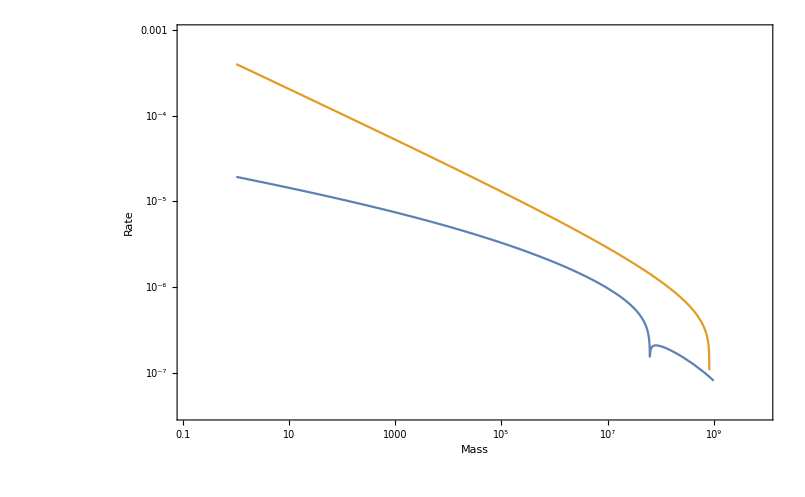

```mathematica
GrowthVStarvationPlot=LogLogPlot[{Re[MortalityOverM],StarvationOverM},{M,1,10^9},Frame->True,FrameLabel->{"Mass","Rate"}]
```

```mathematica
MaintenanceOverM
```

0.000019 M^(3/4)

PLOT ALL RATES TOGETHER

```mathematica
Manipulate[
Show[{
LogLogPlot[{GrowthOverM,
StarvationOverM,
MortalityOverM,
MaintenanceOverM,
RecoveryOverM,
ResourcegrowthOverM/.ALPHA->0.5},{M,0.1,10^8},PlotRange->All],
LogLogPlot[
{InvaderMaintenanceOverM,
InvaderStarvationOverM,
InvaderRecoveryOverM}/.chi->CHI,
{M,0.1,10^8},PlotStyle->Directive[{Dashed,ColorData[97,4]}]]
}],{CHI,-0.5,0.5}]
```

```mathematica
Manipulate[
Show[{
LogPlot[{
(MortalityOverM+RecoveryOverM),
(GrowthOverM*RecoveryOverM),(MortalityOverM*StarvationOverM),
(GrowthOverM*RecoveryOverM),(MortalityOverM*MaintenanceOverM)}/.M->m,
{chi,-0.1,0.1},PlotRange->All],
LogPlot[{
(MortalityOverM+InvaderRecoveryOverM),
(GrowthOverM*InvaderRecoveryOverM),(MortalityOverM*InvaderStarvationOverM),
(GrowthOverM*InvaderRecoveryOverM),(MortalityOverM*InvaderMaintenanceOverM)}/.{M->m},
{chi,-0.1,0.1},PlotStyle->Directive[{Dashed}]]
}],{m,10^5,10^6.5}]
```

```mathematica
Functions={
(MortalityOverM+InvaderRecoveryOverM),
(GrowthOverM*InvaderRecoveryOverM+MortalityOverM*InvaderStarvationOverM),
(GrowthOverM*InvaderRecoveryOverM+MortalityOverM*InvaderMaintenanceOverM)}/.{M->m}
```

{(5.72698×10^-7)/(Log[1.-1.28947 ((1.+chi) m)^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 m^0.19) m)^(1/4)])-(2.29079×10^-6)/Log[1.-(1. (0.324 m^1.01+0.0202 m^1.19))/m],(1.94024×10^-13)/(m^0.206 (Log[1.-1.28947 ((1.+chi) m)^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 m^0.19) m)^(1/4)]))+(5.24772×10^-12)/((Log[1/(1.+chi)]+Log[1.-0.0202 m^0.19]) Log[1.-(1. (0.324 m^1.01+0.0202 m^1.19))/m]),(1.94024×10^-13)/(m^0.206 (Log[1.-1.28947 ((1.+chi) m)^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 m^0.19) m)^(1/4)]))-(4.3525×10^-11 ((1+chi) m)^(3/4))/Log[1.-(1. (0.324 m^1.01+0.0202 m^1.19))/m]}

```mathematica
Plot[Functions,{chi-1,1}]
```

-Graphics-

```mathematica
MortalityOverM
```

-(2.29079×10^-6)/Log[1.-(1. (0.324 M^1.01+0.0202 M^1.19))/M]

```mathematica
Manipulate[
LogLogPlot[{GrowthOverM/(StarvationOverM+MortalityOverM),GrowthOverM/(InvaderStarvationOverM+MortalityOverM)}/.chi->CHI,{M,0.1,10^8},PlotRange->{0.0001,0.1}],
{CHI,-0.5,0.5}]
```

```mathematica
Manipulate[
LogPlot[{ResourcegrowthOverM,MaintenanceOverM/(StarvationOverM-RecoveryOverM),InvaderMaintenanceOverM/(InvaderStarvationOverM-InvaderRecoveryOverM)}/.M->m,{chi,-0.5,0.5},PlotRange->{1,All}],
{m,10^5,10^7}]
```

LogPlot::nonopt: Options expected (instead of {chi, -0.5, 0.5}) beyond position 2 in LogPlot[ResourcegrowthOverM, {MaintenanceOverM/StarvationOverM - RecoveryOverM, InvaderMaintenanceOverM/InvaderStarvationOverM - InvaderRecoveryOverM}/. M → FE`m$$25, {chi, -0.5, 0.5}, PlotRange → {1, All}]. An option must be a rule or a list of rules.

LogPlot::nonopt: Options expected (instead of {chi, -0.5, 0.5}) beyond position 2 in LogPlot[ResourcegrowthOverM, {MaintenanceOverM/StarvationOverM - RecoveryOverM, InvaderMaintenanceOverM/InvaderStarvationOverM - InvaderRecoveryOverM}/. M → FE`m$$39, {chi, -0.5, 0.5}, PlotRange → {1, All}]. An option must be a rule or a list of rules.

```mathematica
FindMinimum[GrowthOverM/(StarvationOverM+MortalityOverM),M]
```

{0.00214181,{M→844888.}}

```mathematica
Solve[MaintenanceOverM==ResourcegrowthOverM,M]
```

{{M→1.9724×10^6 ALPHA^(4/3)}}

```mathematica
InvaderMaintenanceOverM
```

Rf⟦9⟧

```mathematica
Solve[ResourcegrowthOverM==MaintenanceOverM,M]
```

{{M→782748.}}

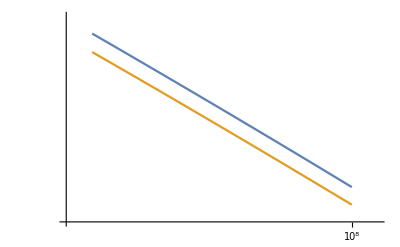

```mathematica
LogLogPlot[{
StarvationOverM,
RecoveryOverM},{M,10^(7.9),10^(8)}]
```

```mathematica
Mvalues=N[RecurrenceTable[{B[n+1] == B[n]+1/50B[n],B[1]==1},B,{n,1,1500}]];
GvSNoise=Table[
parameters={
(*noise*)0.5,
(*ts*)1,
(*M*)Mass =M,
(*B0*)1.9*10^(-2),
(*(*Bm*)0.0245,*)
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
Growth=RF[[1]];
Starvation=RF[[2]];
{M,Growth,Starvation},
{M,Mvalues}];
```

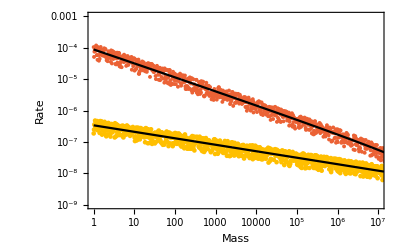

```mathematica
GrowthVStarvationPlot=Show[{
ListLogLogPlot[Transpose[{Re[GvSNoise[[All,1]]],Re[GvSNoise[[All,2]]]}],PlotRange->{{1,10*10^6},{10^(-9),10^(-3)}},Frame->True,PlotStyle->ColorData[97,8],FrameLabel->{"Mass","Rate"}],
ListLogLogPlot[Transpose[{Re[GvSNoise[[All,1]]],Re[GvSNoise[[All,3]]]}],PlotStyle->ColorData[97,4]],
LogLogPlot[GrowthOverM,{M,1,10^10},PlotStyle->Black,PlotRange->All],
LogLogPlot[Re[StarvationOverM],{M,1,10^10},PlotStyle->Black,PlotRange->All]
}]
```

```mathematica
GrowthOverM
```

1.22442×10^-8

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_GvS.pdf",GrowthVStarvationPlot,"PDF",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_GvS.pdf

```mathematica
Recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]
```

```mathematica
Solve[((1-f0*M^(γ-1))==1)/.{f0->0.0202,γ->1.19},M]
```

{{M→0.}}

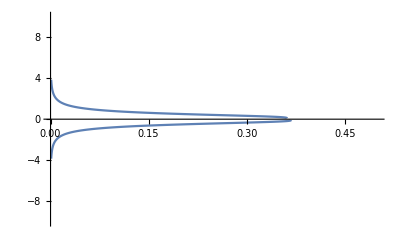

```mathematica
Plot[{-1/Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)],1/Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)]}/.{η->3/4,f0->0.0202,γ->1.19,B0->1.9*10^(-2),Bm->0.0245},{M,0.001,1},PlotRange->{{0,0.5},{-10,10}}]
```

```mathematica
PEQ=-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)]/.{η->3/4,f0->0.0202,γ->1.19,B0->1.9*10^(-2),Bm->0.0245}
```

-Log[1-1.28947 ((1-0.0202 M^0.19) M)^(1/4)]

```mathematica
FindMaximum[Re[PEQ],M]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{19.9662,{M→0.367846}}

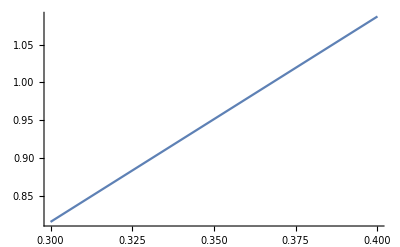

```mathematica
Plot[ M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1))/.{η->3/4,f0->0.0202,γ->1.19,B0->1.9*10^(-2),Bm->0.0245},{M,0.3,0.4}]
```

```mathematica
Solve[((1- (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η))==0)/.{η->3/4,f0->0.0202,γ->1.19,B0->1.9*10^(-2),Bm->0.0245},M]
```

$Aborted

```mathematica
N[(B0/Bm)^(η-1)/.{η->3/4,f0->0.0202,γ->1.19,B0->1.9*10^(-2),Bm->0.0245}]
```

1.06562

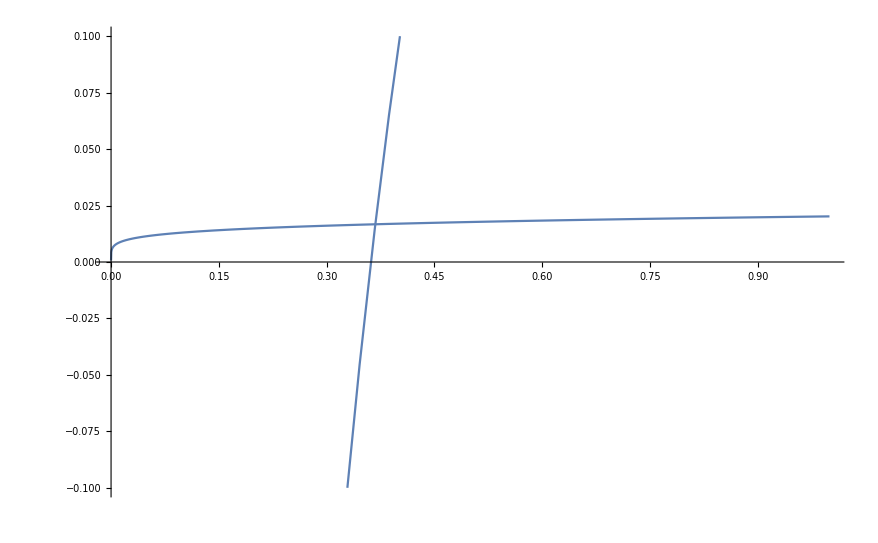

```mathematica
Plot[{(f0*M^(γ-1)),-(1/M)*(B0/Bm)^(1/(1-η))+1}/.{η->3/4,f0->0.0202,γ->1.19,B0->1.9*10^(-2),Bm->0.0245},{M,0,1},PlotRange->{-0.10,0.1}]
```

```mathematica
FullSimplify[1/(B0/Bm)^(1/(η-1))]
```

(B0/Bm)^(1/(1-η))

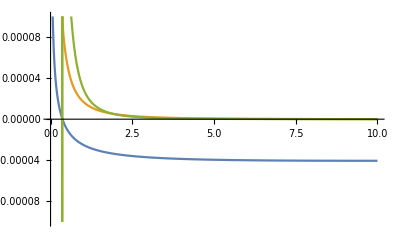

```mathematica
DRecoveryOverM = D[RecoveryOverM,M];
DDRecoveryOverM = D[DRecoveryOverM,M];
Plot[{-RecoveryOverM,DRecoveryOverM,-DDRecoveryOverM},{M,0,10},PlotRange->{-0.0001,0.0001}]
```

What resource growth rate (productivity) would result in the largest observed mammalian body size?
Indricotheriinae:

```mathematica
ClearAll["Global`*"]
```

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
χ=x[[15]];
Growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
Starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
InvaderStarvation =  N[ts*-Bm/(Em*(Log[1-f0*M^(γ-1)] + Log[M/(M*(1+χ))]))]*(1+RandomReal[{-noise,noise}]);
Mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
Recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
InvaderRecovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(1+χ)*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
Maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
InvaderMaintenance = (ts*ef*B0*(M*(1+χ))^η)*(1+RandomReal[{-noise,noise}]);
Resourcegrowth = ts*ALPHA*(1+RandomReal[{-noise,noise}]);

{Growth,Starvation,Mortality,Recovery,Maintenance,Resourcegrowth,InvaderStarvation,InvaderRecovery,InvaderMaintenance}
);
```

```mathematica
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =M,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
GrowthOverM=RF[[1]];
StarvationOverM=RF[[2]];
MortalityOverM = RF[[3]];
MaintenanceOverM = RF[[5]];
RecoveryOverM=RF[[4]];
ResourcegrowthOverM=RF[[6]];
InvaderMaintenanceOverM=RF[[9]];
```

```mathematica
Solve[(ResourcegrowthOverM==MaintenanceOverM)/.M->1.996*10^7,ALPHA]
```

{{ALPHA→5.6738}}

```mathematica
(ResourcegrowthOverM/GrowthOverM)/.{M->1.996*10^7,ALPHA->5.6738}
```

5.34289×10^8